```mathematica
α = 2.321995;
β = 0.7256236;
ψ = 0.5;
```

```mathematica
periodic[amp_, t_] := 1 - amp*Cos[2*Pi*t];
```

```mathematica
SeedRandom[3];
li= RandomVariate[GammaDistribution[(1-ψ)*α, β]];
```

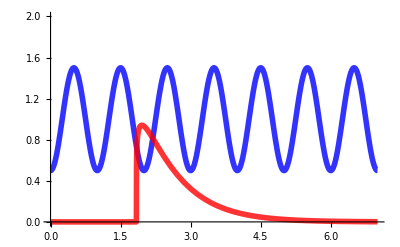

```mathematica
Show[
Plot[periodic[0.5, t],{t,0,7}, PlotRange->{0,2}, PlotStyle->{{Blue, Thickness[0.01], Opacity[0.8]}}],
Plot[PDF[GammaDistribution[ψ α, β], x-li],{x,0,7}, PlotStyle->{{Red, Thickness[0.01], Opacity[0.8]}}]
]
```

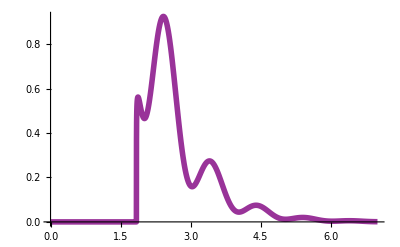

```mathematica
Plot[periodic[0.5, t]*PDF[GammaDistribution[ψ α, β],t-li],{t,0,7}, PlotRange->All, PlotStyle->{{Purple, Thickness[0.01], Opacity[0.8]}}]
```

```mathematica
Mean[ParetoDistribution[10,11,0]]
```

1

```mathematica
Mean[ParetoDistribution[2,3,0]]
```

1

```mathematica
SeedRandom[12];
λ = 2;
pareto1 = 2;
pareto2 = 3;
nchanges = RandomVariate[PoissonDistribution[7*λ]];
tchanges = Sort[RandomVariate[UniformDistribution[{0,7}], nchanges]];
```

```mathematica
tchanges;
```

```mathematica
ranges = {Join[{0},tchanges], Join[tchanges,{7}]}ᵀ;
```

```mathematica
cvals = RandomVariate[ParetoDistribution[pareto1,pareto2,0],Length[ranges]];
```

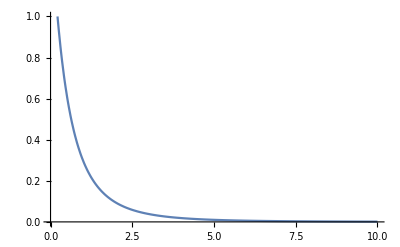

```mathematica
Plot[PDF[ParetoDistribution[pareto1,pareto2,0],x],{x,0,10}, PlotRange->{0,1}]
```

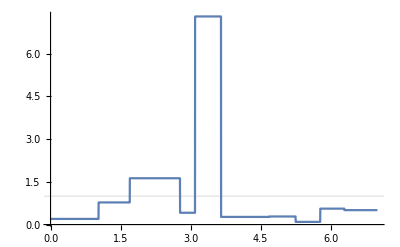

```mathematica
Plot[Piecewise[Table[
{cvals[[i]], x >= ranges[[i,1]] && x < ranges[[i,2]]}, {i,Length[ranges]}
]],{x,0,7}, PlotRange->{0, All}, GridLines->{{},{{1, {Dashed, Opacity[1]}}}}]
```

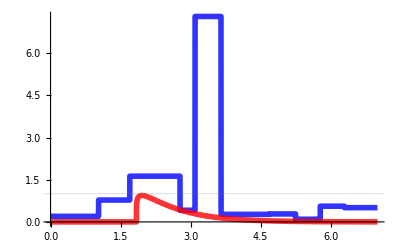

```mathematica
Show[
Plot[Piecewise[Table[
{cvals[[i]], x >= ranges[[i,1]] && x < ranges[[i,2]]}, {i,Length[ranges]}
]],{x,0,7}, PlotRange->{0, All}, PlotStyle->{Blue, Thickness[0.01], Opacity[0.8]}, GridLines->{{},{{1, {Dashed, Opacity[1]}}}}],
Plot[PDF[GammaDistribution[ψ α, β], x-li],{x,0,7}, PlotStyle->{{Red, Thickness[0.01], Opacity[0.8]}}]
]
```